```mathematica
reprate=10
increaseRate=0.3333
normalPowerIncrease=10000
lowpowerIncreaseRateLimit=1000000
lowpowerincrease=1000;
powerIncrease1[pulse_]:=Piecewise[{{pulse/(lowpowerIncreaseRateLimit/(increaseRate*normalPowerIncrease)),pulse<lowpowerIncreaseRateLimit/increaseRate}},normalPowerIncrease]
powerIncrease[pulse_]:=Ceiling[powerIncrease1[pulse],lowpowerincrease]
power[pulse_]:=Ceiling[pulse*increaseRate,powerIncrease[pulse]]
```

10

0.3333

10000

1000000

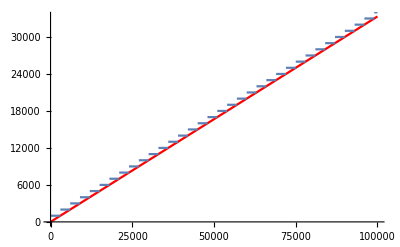

```mathematica
Show[{Plot[increaseRate x,{x,0,10^5},PlotStyle->Red],
Plot[power[x], {x,0,100000}, PlotPoints->20000, MaxRecursion->2, AxesLabel->{"pulse number","power (W)"}]}]
```

```mathematica
Ceiling[Piecewise[{{pulse/(linearIncreaseRateLimit0/(increaseRate0*normalPowerIncrease0)),pulse<linearIncreaseRateLimit0/increaseRate0}},normalPowerIncrease0],lowpowerincrease0]
```

Ceiling[Piecewise[{{(increaseRate0 normalPowerIncrease0 pulse)/linearIncreaseRateLimit0, pulse<linearIncreaseRateLimit0/increaseRate0}, {normalPowerIncrease0, True}}],lowpowerincrease0]

```mathematica
repRate=10(*RF repetition rate*);
(*minPulses=5000 (*minimum number of pulses at a power before increasing? might not need this*);*)
increaseRate=10000/30000 (*rate aim in W per pulse*);
```

```mathematica
time[pulse_]:=pulse/repRate (*time in seconds at pulse number*);
timeIncreaseRate=10000./time[30000] (*rate aim in W per second*)
```

3.33333

```mathematica
shortTimeAim=aim*0.2/timeIncreaseRate
```

600000.

```mathematica
Clear[powerIncrease]
normalPowerIncrease=10000(*the normal amount to increase the power*);
linearIncreaseRateLimit=1000000 (*go up to this power (in W)in linear steps*);
dp=1000;
powerIncrease[pulse_]:=Ceiling[Piecewise[{{pulse/(linearIncreaseRateLimit/(increaseRate*normalPowerIncrease)),pulse<linearIncreaseRateLimit/increaseRate}},normalPowerIncrease],dp](*Power increase step or function*);
```

```mathematica
Piecewise[{{pulse/(linearIncreaseRateLimit/(increaseRate*normalPowerIncrease)),pulse<linearIncreaseRateLimit/increaseRate}},normalPowerIncrease]
```

Piecewise[{{pulse/300, pulse<3000000}, {10000, True}}]

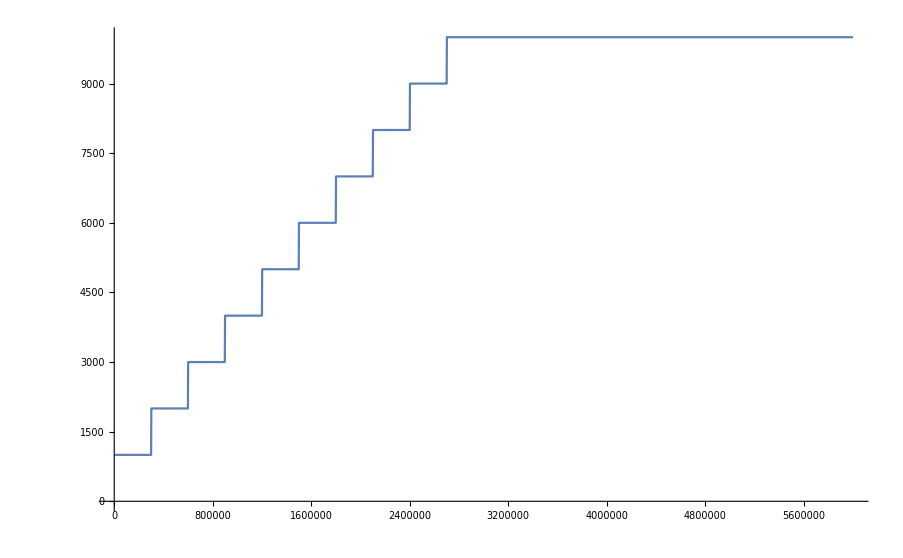

```mathematica
Plot[powerIncrease[x], {x,0,6000000}]
```

```mathematica
Clear[ power]
power[pulse_]:=Ceiling[pulse*increaseRate,powerIncrease[pulse]]
```

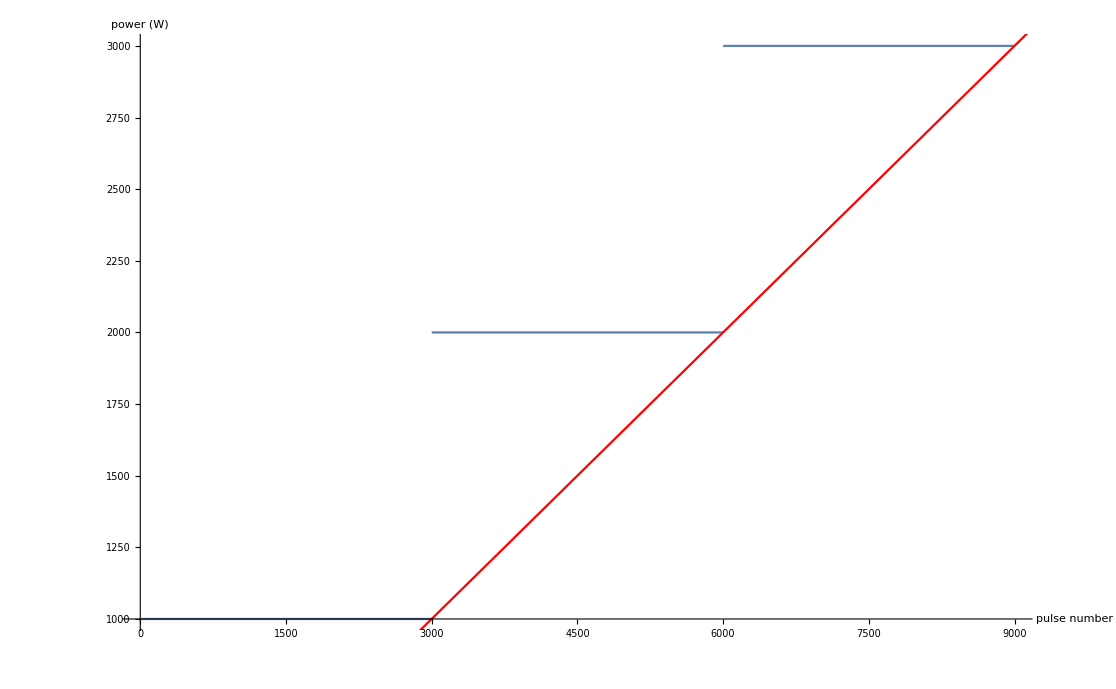

```mathematica
Show[{Plot[power[x], {x,0,9000}, PlotPoints->20000, MaxRecursion->2, AxesLabel->{"pulse number","power (W)"}]
,Plot[increaseRate x,{x,0,10^4},PlotStyle->Red]
}]
```

```mathematica
power[30 10^6]
```

10000000

```mathematica
T0=AbsoluteTime[];
pulsepowerdat=Table[{x,power[x]},{x,1,30 10^6,1}];
AbsoluteTime[]-T0
```

45.804

```mathematica
indices=(#&/@SplitBy[pulsepowerdat,Last]);
```

```mathematica
Table[indices⟦i⟧⟦-1⟧,{i,1,Length@indices}]
```

{{3000,1000},{6000,2000},{9000,3000},{12000,4000},{15000,5000},{18000,6000},{21000,7000},{24000,8000},{27000,9000},{30000,10000},{33000,11000},{36000,12000},{39000,13000},{42000,14000},{45000,15000},{48000,16000},{51000,17000},{54000,18000},{57000,19000},{60000,20000},{63000,21000},{66000,22000},{69000,23000},{72000,24000},{75000,25000},{78000,26000},{81000,27000},{84000,28000},{87000,29000},{90000,30000},{93000,31000},{96000,32000},{99000,33000},{102000,34000},{105000,35000},{108000,36000},{111000,37000},{114000,38000},{117000,39000},{120000,40000},{123000,41000},{126000,42000},{129000,43000},{132000,44000},{135000,45000},{138000,46000},{141000,47000},{144000,48000},{147000,49000},{150000,50000},{153000,51000},{156000,52000},{159000,53000},{162000,54000},{165000,55000},{168000,56000},{171000,57000},{174000,58000},{177000,59000},{180000,60000},{183000,61000},{186000,62000},{189000,63000},{192000,64000},{195000,65000},{198000,66000},{201000,67000},{204000,68000},{207000,69000},{210000,70000},{213000,71000},{216000,72000},{219000,73000},{222000,74000},{225000,75000},{228000,76000},{231000,77000},{234000,78000},{237000,79000},{240000,80000},{243000,81000},{246000,82000},{249000,83000},{252000,84000},{255000,85000},{258000,86000},{261000,87000},{264000,88000},{267000,89000},{270000,90000},{273000,91000},{276000,92000},{279000,93000},{282000,94000},{285000,95000},{288000,96000},{291000,97000},{294000,98000},{297000,99000},{300000,100000},{306000,102000},{312000,104000},{318000,106000},{324000,108000},{330000,110000},{336000,112000},{342000,114000},{348000,116000},{354000,118000},{360000,120000},{366000,122000},{372000,124000},{378000,126000},{384000,128000},{390000,130000},{396000,132000},{402000,134000},{408000,136000},{414000,138000},{420000,140000},{426000,142000},{432000,144000},{438000,146000},{444000,148000},{450000,150000},{456000,152000},{462000,154000},{468000,156000},{474000,158000},{480000,160000},{486000,162000},{492000,164000},{498000,166000},{504000,168000},{510000,170000},{516000,172000},{522000,174000},{528000,176000},{534000,178000},{540000,180000},{546000,182000},{552000,184000},{558000,186000},{564000,188000},{570000,190000},{576000,192000},{582000,194000},{588000,196000},{594000,198000},{600000,200000},{603000,201000},{612000,204000},{621000,207000},{630000,210000},{639000,213000},{648000,216000},{657000,219000},{666000,222000},{675000,225000},{684000,228000},{693000,231000},{702000,234000},{711000,237000},{720000,240000},{729000,243000},{738000,246000},{747000,249000},{756000,252000},{765000,255000},{774000,258000},{783000,261000},{792000,264000},{801000,267000},{810000,270000},{819000,273000},{828000,276000},{837000,279000},{846000,282000},{855000,285000},{864000,288000},{873000,291000},{882000,294000},{891000,297000},{900000,300000},{912000,304000},{924000,308000},{936000,312000},{948000,316000},{960000,320000},{972000,324000},{984000,328000},{996000,332000},{1008000,336000},{1020000,340000},{1032000,344000},{1044000,348000},{1056000,352000},{1068000,356000},{1080000,360000},{1092000,364000},{1104000,368000},{1116000,372000},{1128000,376000},{1140000,380000},{1152000,384000},{1164000,388000},{1176000,392000},{1188000,396000},{1200000,400000},{1215000,405000},{1230000,410000},{1245000,415000},{1260000,420000},{1275000,425000},{1290000,430000},{1305000,435000},{1320000,440000},{1335000,445000},{1350000,450000},{1365000,455000},{1380000,460000},{1395000,465000},{1410000,470000},{1425000,475000},{1440000,480000},{1455000,485000},{1470000,490000},{1485000,495000},{1500000,500000},{1512000,504000},{1530000,510000},{1548000,516000},{1566000,522000},{1584000,528000},{1602000,534000},{1620000,540000},{1638000,546000},{1656000,552000},{1674000,558000},{1692000,564000},{1710000,570000},{1728000,576000},{1746000,582000},{1764000,588000},{1782000,594000},{1800000,600000},{1806000,602000},{1827000,609000},{1848000,616000},{1869000,623000},{1890000,630000},{1911000,637000},{1932000,644000},{1953000,651000},{1974000,658000},{1995000,665000},{2016000,672000},{2037000,679000},{2058000,686000},{2079000,693000},{2100000,700000},{2112000,704000},{2136000,712000},{2160000,720000},{2184000,728000},{2208000,736000},{2232000,744000},{2256000,752000},{2280000,760000},{2304000,768000},{2328000,776000},{2352000,784000},{2376000,792000},{2400000,800000},{2403000,801000},{2430000,810000},{2457000,819000},{2484000,828000},{2511000,837000},{2538000,846000},{2565000,855000},{2592000,864000},{2619000,873000},{2646000,882000},{2673000,891000},{2700000,900000},{2730000,910000},{2760000,920000},{2790000,930000},{2820000,940000},{2850000,950000},{2880000,960000},{2910000,970000},{2940000,980000},{2970000,990000},{3000000,1000000},{3030000,1010000},{3060000,1020000},{3090000,1030000},{3120000,1040000},{3150000,1050000},{3180000,1060000},{3210000,1070000},{3240000,1080000},{3270000,1090000},{3300000,1100000},{3330000,1110000},{3360000,1120000},{3390000,1130000},{3420000,1140000},{3450000,1150000},{3480000,1160000},{3510000,1170000},{3540000,1180000},{3570000,1190000},{3600000,1200000},{3630000,1210000},{3660000,1220000},{3690000,1230000},{3720000,1240000},{3750000,1250000},{3780000,1260000},{3810000,1270000},{3840000,1280000},{3870000,1290000},{3900000,1300000},{3930000,1310000},{3960000,1320000},{3990000,1330000},{4020000,1340000},{4050000,1350000},{4080000,1360000},{4110000,1370000},{4140000,1380000},{4170000,1390000},{4200000,1400000},{4230000,1410000},{4260000,1420000},{4290000,1430000},{4320000,1440000},{4350000,1450000},{4380000,1460000},{4410000,1470000},{4440000,1480000},{4470000,1490000},{4500000,1500000},{4530000,1510000},{4560000,1520000},{4590000,1530000},{4620000,1540000},{4650000,1550000},{4680000,1560000},{4710000,1570000},{4740000,1580000},{4770000,1590000},{4800000,1600000},{4830000,1610000},{4860000,1620000},{4890000,1630000},{4920000,1640000},{4950000,1650000},{4980000,1660000},{5010000,1670000},{5040000,1680000},{5070000,1690000},{5100000,1700000},{5130000,1710000},{5160000,1720000},{5190000,1730000},{5220000,1740000},{5250000,1750000},{5280000,1760000},{5310000,1770000},{5340000,1780000},{5370000,1790000},{5400000,1800000},{5430000,1810000},{5460000,1820000},{5490000,1830000},{5520000,1840000},{5550000,1850000},{5580000,1860000},{5610000,1870000},{5640000,1880000},{5670000,1890000},{5700000,1900000},{5730000,1910000},{5760000,1920000},{5790000,1930000},{5820000,1940000},{5850000,1950000},{5880000,1960000},{5910000,1970000},{5940000,1980000},{5970000,1990000},{6000000,2000000},{6030000,2010000},{6060000,2020000},{6090000,2030000},{6120000,2040000},{6150000,2050000},{6180000,2060000},{6210000,2070000},{6240000,2080000},{6270000,2090000},{6300000,2100000},{6330000,2110000},{6360000,2120000},{6390000,2130000},{6420000,2140000},{6450000,2150000},{6480000,2160000},{6510000,2170000},{6540000,2180000},{6570000,2190000},{6600000,2200000},{6630000,2210000},{6660000,2220000},{6690000,2230000},{6720000,2240000},{6750000,2250000},{6780000,2260000},{6810000,2270000},{6840000,2280000},{6870000,2290000},{6900000,2300000},{6930000,2310000},{6960000,2320000},{6990000,2330000},{7020000,2340000},{7050000,2350000},{7080000,2360000},{7110000,2370000},{7140000,2380000},{7170000,2390000},{7200000,2400000},{7230000,2410000},{7260000,2420000},{7290000,2430000},{7320000,2440000},{7350000,2450000},{7380000,2460000},{7410000,2470000},{7440000,2480000},{7470000,2490000},{7500000,2500000},{7530000,2510000},{7560000,2520000},{7590000,2530000},{7620000,2540000},{7650000,2550000},{7680000,2560000},{7710000,2570000},{7740000,2580000},{7770000,2590000},{7800000,2600000},{7830000,2610000},{7860000,2620000},{7890000,2630000},{7920000,2640000},{7950000,2650000},{7980000,2660000},{8010000,2670000},{8040000,2680000},{8070000,2690000},{8100000,2700000},{8130000,2710000},{8160000,2720000},{8190000,2730000},{8220000,2740000},{8250000,2750000},{8280000,2760000},{8310000,2770000},{8340000,2780000},{8370000,2790000},{8400000,2800000},{8430000,2810000},{8460000,2820000},{8490000,2830000},{8520000,2840000},{8550000,2850000},{8580000,2860000},{8610000,2870000},{8640000,2880000},{8670000,2890000},{8700000,2900000},{8730000,2910000},{8760000,2920000},{8790000,2930000},{8820000,2940000},{8850000,2950000},{8880000,2960000},{8910000,2970000},{8940000,2980000},{8970000,2990000},{9000000,3000000},{9030000,3010000},{9060000,3020000},{9090000,3030000},{9120000,3040000},{9150000,3050000},{9180000,3060000},{9210000,3070000},{9240000,3080000},{9270000,3090000},{9300000,3100000},{9330000,3110000},{9360000,3120000},{9390000,3130000},{9420000,3140000},{9450000,3150000},{9480000,3160000},{9510000,3170000},{9540000,3180000},{9570000,3190000},{9600000,3200000},{9630000,3210000},{9660000,3220000},{9690000,3230000},{9720000,3240000},{9750000,3250000},{9780000,3260000},{9810000,3270000},{9840000,3280000},{9870000,3290000},{9900000,3300000},{9930000,3310000},{9960000,3320000},{9990000,3330000},{10000000,3340000}}

```mathematica
indices⟦All,-1⟧⟦All,2⟧
```

{1000,2000,3000,4000,5000,6000,7000,8000,9000,10000,11000,12000,13000,14000,15000,16000,17000,18000,19000,20000,21000,22000,23000,24000,25000,26000,27000,28000,29000,30000,31000,32000,33000,34000,35000,36000,37000,38000,39000,40000,41000,42000,43000,44000,45000,46000,47000,48000,49000,50000,51000,52000,53000,54000,55000,56000,57000,58000,59000,60000,61000,62000,63000,64000,65000,66000,67000,68000,69000,70000,71000,72000,73000,74000,75000,76000,77000,78000,79000,80000,81000,82000,83000,84000,85000,86000,87000,88000,89000,90000,91000,92000,93000,94000,95000,96000,97000,98000,99000,100000,102000,104000,106000,108000,110000,112000,114000,116000,118000,120000,122000,124000,126000,128000,130000,132000,134000,136000,138000,140000,142000,144000,146000,148000,150000,152000,154000,156000,158000,160000,162000,164000,166000,168000,170000,172000,174000,176000,178000,180000,182000,184000,186000,188000,190000,192000,194000,196000,198000,200000,201000,204000,207000,210000,213000,216000,219000,222000,225000,228000,231000,234000,237000,240000,243000,246000,249000,252000,255000,258000,261000,264000,267000,270000,273000,276000,279000,282000,285000,288000,291000,294000,297000,300000,304000,308000,312000,316000,320000,324000,328000,332000,336000,340000,344000,348000,352000,356000,360000,364000,368000,372000,376000,380000,384000,388000,392000,396000,400000,405000,410000,415000,420000,425000,430000,435000,440000,445000,450000,455000,460000,465000,470000,475000,480000,485000,490000,495000,500000,504000,510000,516000,522000,528000,534000,540000,546000,552000,558000,564000,570000,576000,582000,588000,594000,600000,602000,609000,616000,623000,630000,637000,644000,651000,658000,665000,672000,679000,686000,693000,700000,704000,712000,720000,728000,736000,744000,752000,760000,768000,776000,784000,792000,800000,801000,810000,819000,828000,837000,846000,855000,864000,873000,882000,891000,900000,910000,920000,930000,940000,950000,960000,970000,980000,990000,1000000,1010000,1020000,1030000,1040000,1050000,1060000,1070000,1080000,1090000,1100000,1110000,1120000,1130000,1140000,1150000,1160000,1170000,1180000,1190000,1200000,1210000,1220000,1230000,1240000,1250000,1260000,1270000,1280000,1290000,1300000,1310000,1320000,1330000,1340000,1350000,1360000,1370000,1380000,1390000,1400000,1410000,1420000,1430000,1440000,1450000,1460000,1470000,1480000,1490000,1500000,1510000,1520000,1530000,1540000,1550000,1560000,1570000,1580000,1590000,1600000,1610000,1620000,1630000,1640000,1650000,1660000,1670000,1680000,1690000,1700000,1710000,1720000,1730000,1740000,1750000,1760000,1770000,1780000,1790000,1800000,1810000,1820000,1830000,1840000,1850000,1860000,1870000,1880000,1890000,1900000,1910000,1920000,1930000,1940000,1950000,1960000,1970000,1980000,1990000,2000000,2010000,2020000,2030000,2040000,2050000,2060000,2070000,2080000,2090000,2100000,2110000,2120000,2130000,2140000,2150000,2160000,2170000,2180000,2190000,2200000,2210000,2220000,2230000,2240000,2250000,2260000,2270000,2280000,2290000,2300000,2310000,2320000,2330000,2340000,2350000,2360000,2370000,2380000,2390000,2400000,2410000,2420000,2430000,2440000,2450000,2460000,2470000,2480000,2490000,2500000,2510000,2520000,2530000,2540000,2550000,2560000,2570000,2580000,2590000,2600000,2610000,2620000,2630000,2640000,2650000,2660000,2670000,2680000,2690000,2700000,2710000,2720000,2730000,2740000,2750000,2760000,2770000,2780000,2790000,2800000,2810000,2820000,2830000,2840000,2850000,2860000,2870000,2880000,2890000,2900000,2910000,2920000,2930000,2940000,2950000,2960000,2970000,2980000,2990000,3000000,3010000,3020000,3030000,3040000,3050000,3060000,3070000,3080000,3090000,3100000,3110000,3120000,3130000,3140000,3150000,3160000,3170000,3180000,3190000,3200000,3210000,3220000,3230000,3240000,3250000,3260000,3270000,3280000,3290000,3300000,3310000,3320000,3330000,3340000}

```mathematica
AMPSETlist=Transpose[{indices⟦All,-1⟧⟦All,2⟧,
Join[{indices⟦All,-1⟧⟦1,1⟧},Differences[indices⟦All,-1⟧⟦All,1⟧]]
}]
```

{{1000,3000},{2000,3000},{3000,3000},{4000,3000},{5000,3000},{6000,3000},{7000,3000},{8000,3000},{9000,3000},{10000,3000},{11000,3000},{12000,3000},{13000,3000},{14000,3000},{15000,3000},{16000,3000},{17000,3000},{18000,3000},{19000,3000},{20000,3000},{21000,3000},{22000,3000},{23000,3000},{24000,3000},{25000,3000},{26000,3000},{27000,3000},{28000,3000},{29000,3000},{30000,3000},{31000,3000},{32000,3000},{33000,3000},{34000,3000},{35000,3000},{36000,3000},{37000,3000},{38000,3000},{39000,3000},{40000,3000},{41000,3000},{42000,3000},{43000,3000},{44000,3000},{45000,3000},{46000,3000},{47000,3000},{48000,3000},{49000,3000},{50000,3000},{51000,3000},{52000,3000},{53000,3000},{54000,3000},{55000,3000},{56000,3000},{57000,3000},{58000,3000},{59000,3000},{60000,3000},{61000,3000},{62000,3000},{63000,3000},{64000,3000},{65000,3000},{66000,3000},{67000,3000},{68000,3000},{69000,3000},{70000,3000},{71000,3000},{72000,3000},{73000,3000},{74000,3000},{75000,3000},{76000,3000},{77000,3000},{78000,3000},{79000,3000},{80000,3000},{81000,3000},{82000,3000},{83000,3000},{84000,3000},{85000,3000},{86000,3000},{87000,3000},{88000,3000},{89000,3000},{90000,3000},{91000,3000},{92000,3000},{93000,3000},{94000,3000},{95000,3000},{96000,3000},{97000,3000},{98000,3000},{99000,3000},{100000,3000},{102000,6000},{104000,6000},{106000,6000},{108000,6000},{110000,6000},{112000,6000},{114000,6000},{116000,6000},{118000,6000},{120000,6000},{122000,6000},{124000,6000},{126000,6000},{128000,6000},{130000,6000},{132000,6000},{134000,6000},{136000,6000},{138000,6000},{140000,6000},{142000,6000},{144000,6000},{146000,6000},{148000,6000},{150000,6000},{152000,6000},{154000,6000},{156000,6000},{158000,6000},{160000,6000},{162000,6000},{164000,6000},{166000,6000},{168000,6000},{170000,6000},{172000,6000},{174000,6000},{176000,6000},{178000,6000},{180000,6000},{182000,6000},{184000,6000},{186000,6000},{188000,6000},{190000,6000},{192000,6000},{194000,6000},{196000,6000},{198000,6000},{200000,6000},{201000,3000},{204000,9000},{207000,9000},{210000,9000},{213000,9000},{216000,9000},{219000,9000},{222000,9000},{225000,9000},{228000,9000},{231000,9000},{234000,9000},{237000,9000},{240000,9000},{243000,9000},{246000,9000},{249000,9000},{252000,9000},{255000,9000},{258000,9000},{261000,9000},{264000,9000},{267000,9000},{270000,9000},{273000,9000},{276000,9000},{279000,9000},{282000,9000},{285000,9000},{288000,9000},{291000,9000},{294000,9000},{297000,9000},{300000,9000},{304000,12000},{308000,12000},{312000,12000},{316000,12000},{320000,12000},{324000,12000},{328000,12000},{332000,12000},{336000,12000},{340000,12000},{344000,12000},{348000,12000},{352000,12000},{356000,12000},{360000,12000},{364000,12000},{368000,12000},{372000,12000},{376000,12000},{380000,12000},{384000,12000},{388000,12000},{392000,12000},{396000,12000},{400000,12000},{405000,15000},{410000,15000},{415000,15000},{420000,15000},{425000,15000},{430000,15000},{435000,15000},{440000,15000},{445000,15000},{450000,15000},{455000,15000},{460000,15000},{465000,15000},{470000,15000},{475000,15000},{480000,15000},{485000,15000},{490000,15000},{495000,15000},{500000,15000},{504000,12000},{510000,18000},{516000,18000},{522000,18000},{528000,18000},{534000,18000},{540000,18000},{546000,18000},{552000,18000},{558000,18000},{564000,18000},{570000,18000},{576000,18000},{582000,18000},{588000,18000},{594000,18000},{600000,18000},{602000,6000},{609000,21000},{616000,21000},{623000,21000},{630000,21000},{637000,21000},{644000,21000},{651000,21000},{658000,21000},{665000,21000},{672000,21000},{679000,21000},{686000,21000},{693000,21000},{700000,21000},{704000,12000},{712000,24000},{720000,24000},{728000,24000},{736000,24000},{744000,24000},{752000,24000},{760000,24000},{768000,24000},{776000,24000},{784000,24000},{792000,24000},{800000,24000},{801000,3000},{810000,27000},{819000,27000},{828000,27000},{837000,27000},{846000,27000},{855000,27000},{864000,27000},{873000,27000},{882000,27000},{891000,27000},{900000,27000},{910000,30000},{920000,30000},{930000,30000},{940000,30000},{950000,30000},{960000,30000},{970000,30000},{980000,30000},{990000,30000},{1000000,30000},{1010000,30000},{1020000,30000},{1030000,30000},{1040000,30000},{1050000,30000},{1060000,30000},{1070000,30000},{1080000,30000},{1090000,30000},{1100000,30000},{1110000,30000},{1120000,30000},{1130000,30000},{1140000,30000},{1150000,30000},{1160000,30000},{1170000,30000},{1180000,30000},{1190000,30000},{1200000,30000},{1210000,30000},{1220000,30000},{1230000,30000},{1240000,30000},{1250000,30000},{1260000,30000},{1270000,30000},{1280000,30000},{1290000,30000},{1300000,30000},{1310000,30000},{1320000,30000},{1330000,30000},{1340000,30000},{1350000,30000},{1360000,30000},{1370000,30000},{1380000,30000},{1390000,30000},{1400000,30000},{1410000,30000},{1420000,30000},{1430000,30000},{1440000,30000},{1450000,30000},{1460000,30000},{1470000,30000},{1480000,30000},{1490000,30000},{1500000,30000},{1510000,30000},{1520000,30000},{1530000,30000},{1540000,30000},{1550000,30000},{1560000,30000},{1570000,30000},{1580000,30000},{1590000,30000},{1600000,30000},{1610000,30000},{1620000,30000},{1630000,30000},{1640000,30000},{1650000,30000},{1660000,30000},{1670000,30000},{1680000,30000},{1690000,30000},{1700000,30000},{1710000,30000},{1720000,30000},{1730000,30000},{1740000,30000},{1750000,30000},{1760000,30000},{1770000,30000},{1780000,30000},{1790000,30000},{1800000,30000},{1810000,30000},{1820000,30000},{1830000,30000},{1840000,30000},{1850000,30000},{1860000,30000},{1870000,30000},{1880000,30000},{1890000,30000},{1900000,30000},{1910000,30000},{1920000,30000},{1930000,30000},{1940000,30000},{1950000,30000},{1960000,30000},{1970000,30000},{1980000,30000},{1990000,30000},{2000000,30000},{2010000,30000},{2020000,30000},{2030000,30000},{2040000,30000},{2050000,30000},{2060000,30000},{2070000,30000},{2080000,30000},{2090000,30000},{2100000,30000},{2110000,30000},{2120000,30000},{2130000,30000},{2140000,30000},{2150000,30000},{2160000,30000},{2170000,30000},{2180000,30000},{2190000,30000},{2200000,30000},{2210000,30000},{2220000,30000},{2230000,30000},{2240000,30000},{2250000,30000},{2260000,30000},{2270000,30000},{2280000,30000},{2290000,30000},{2300000,30000},{2310000,30000},{2320000,30000},{2330000,30000},{2340000,30000},{2350000,30000},{2360000,30000},{2370000,30000},{2380000,30000},{2390000,30000},{2400000,30000},{2410000,30000},{2420000,30000},{2430000,30000},{2440000,30000},{2450000,30000},{2460000,30000},{2470000,30000},{2480000,30000},{2490000,30000},{2500000,30000},{2510000,30000},{2520000,30000},{2530000,30000},{2540000,30000},{2550000,30000},{2560000,30000},{2570000,30000},{2580000,30000},{2590000,30000},{2600000,30000},{2610000,30000},{2620000,30000},{2630000,30000},{2640000,30000},{2650000,30000},{2660000,30000},{2670000,30000},{2680000,30000},{2690000,30000},{2700000,30000},{2710000,30000},{2720000,30000},{2730000,30000},{2740000,30000},{2750000,30000},{2760000,30000},{2770000,30000},{2780000,30000},{2790000,30000},{2800000,30000},{2810000,30000},{2820000,30000},{2830000,30000},{2840000,30000},{2850000,30000},{2860000,30000},{2870000,30000},{2880000,30000},{2890000,30000},{2900000,30000},{2910000,30000},{2920000,30000},{2930000,30000},{2940000,30000},{2950000,30000},{2960000,30000},{2970000,30000},{2980000,30000},{2990000,30000},{3000000,30000},{3010000,30000},{3020000,30000},{3030000,30000},{3040000,30000},{3050000,30000},{3060000,30000},{3070000,30000},{3080000,30000},{3090000,30000},{3100000,30000},{3110000,30000},{3120000,30000},{3130000,30000},{3140000,30000},{3150000,30000},{3160000,30000},{3170000,30000},{3180000,30000},{3190000,30000},{3200000,30000},{3210000,30000},{3220000,30000},{3230000,30000},{3240000,30000},{3250000,30000},{3260000,30000},{3270000,30000},{3280000,30000},{3290000,30000},{3300000,30000},{3310000,30000},{3320000,30000},{3330000,30000},{3340000,10000}}

```mathematica
Differences@indices⟦All,1⟧⟦All,1⟧
Join[indices⟦All,1⟧⟦All,2⟧,{indices⟦-1,-1,1⟧}]
```

{3000,3000,3000,3000,3000,3000,3000,3000,3000,3000,3000,3000,3000,3000,3000,3000,3000,3000,3000,3000,3000,3000,3000,3000,3000,3000,3000,3000,3000,3000,3000,3000,3000,3000,3000,3000,3000,3000,3000,3000,3000,3000,3000,3000,3000,3000,3000,3000,3000,3000,3000,3000,3000,3000,3000,3000,3000,3000,3000,3000,3000,3000,3000,3000,3000,3000,3000,3000,3000,3000,3000,3000,3000,3000,3000,3000,3000,3000,3000,3000,3000,3000,3000,3000,3000,3000,3000,3000,3000,3000,3000,3000,3000,3000,3000,3000,3000,3000,3000,3000,6000,6000,6000,6000,6000,6000,6000,6000,6000,6000,6000,6000,6000,6000,6000,6000,6000,6000,6000,6000,6000,6000,6000,6000,6000,6000,6000,6000,6000,6000,6000,6000,6000,6000,6000,6000,6000,6000,6000,6000,6000,6000,6000,6000,6000,6000,6000,6000,6000,6000,3000,9000,9000,9000,9000,9000,9000,9000,9000,9000,9000,9000,9000,9000,9000,9000,9000,9000,9000,9000,9000,9000,9000,9000,9000,9000,9000,9000,9000,9000,9000,9000,9000,9000,12000,12000,12000,12000,12000,12000,12000,12000,12000,12000,12000,12000,12000,12000,12000,12000,12000,12000,12000,12000,12000,12000,12000,12000,12000,15000,15000,15000,15000,15000,15000,15000,15000,15000,15000,15000,15000,15000,15000,15000,15000,15000,15000,15000,15000,12000,18000,18000,18000,18000,18000,18000,18000,18000,18000,18000,18000,18000,18000,18000,18000,18000,6000,21000,21000,21000,21000,21000,21000,21000,21000,21000,21000,21000,21000,21000,21000,12000,24000,24000,24000,24000,24000,24000,24000,24000,24000,24000,24000,24000,3000,27000,27000,27000,27000,27000,27000,27000,27000,27000,27000,27000,30000,30000,30000,30000,30000,30000,30000,30000,30000,30000,30000,30000,30000,30000,30000,30000,30000,30000,30000,30000,30000,30000,30000,30000,30000,30000,30000,30000,30000,30000,30000,30000,30000,30000,30000,30000,30000,30000,30000,30000,30000,30000,30000,30000,30000,30000,30000,30000,30000,30000,30000,30000,30000,30000,30000,30000,30000,30000,30000,30000,30000,30000,30000,30000,30000,30000,30000,30000,30000,30000,30000,30000,30000,30000,30000,30000,30000,30000,30000,30000,30000,30000,30000,30000,30000,30000,30000,30000,30000,30000,30000,30000,30000,30000,30000,30000,30000,30000,30000,30000,30000,30000,30000,30000,30000,30000,30000,30000,30000,30000,30000,30000,30000,30000,30000,30000,30000,30000,30000,30000,30000,30000,30000,30000,30000,30000,30000,30000,30000,30000,30000,30000,30000,30000,30000,30000,30000,30000,30000,30000,30000,30000,30000,30000,30000,30000,30000,30000,30000,30000,30000,30000,30000,30000,30000,30000,30000,30000,30000,30000,30000,30000,30000,30000,30000,30000,30000,30000,30000,30000,30000,30000,30000,30000,30000,30000,30000,30000,30000,30000,30000,30000,30000,30000,30000,30000,30000,30000,30000,30000,30000,30000,30000,30000,30000,30000,30000,30000,30000,30000,30000,30000,30000,30000,30000,30000,30000,30000,30000,30000,30000,30000,30000,30000,30000,30000,30000,30000,30000,30000,30000,30000,30000,30000,30000,30000,30000,30000,30000,30000,30000,30000,30000,30000,30000,30000,30000,30000,30000,30000,30000,30000,30000}

{1000,2000,3000,4000,5000,6000,7000,8000,9000,10000,11000,12000,13000,14000,15000,16000,17000,18000,19000,20000,21000,22000,23000,24000,25000,26000,27000,28000,29000,30000,31000,32000,33000,34000,35000,36000,37000,38000,39000,40000,41000,42000,43000,44000,45000,46000,47000,48000,49000,50000,51000,52000,53000,54000,55000,56000,57000,58000,59000,60000,61000,62000,63000,64000,65000,66000,67000,68000,69000,70000,71000,72000,73000,74000,75000,76000,77000,78000,79000,80000,81000,82000,83000,84000,85000,86000,87000,88000,89000,90000,91000,92000,93000,94000,95000,96000,97000,98000,99000,100000,102000,104000,106000,108000,110000,112000,114000,116000,118000,120000,122000,124000,126000,128000,130000,132000,134000,136000,138000,140000,142000,144000,146000,148000,150000,152000,154000,156000,158000,160000,162000,164000,166000,168000,170000,172000,174000,176000,178000,180000,182000,184000,186000,188000,190000,192000,194000,196000,198000,200000,201000,204000,207000,210000,213000,216000,219000,222000,225000,228000,231000,234000,237000,240000,243000,246000,249000,252000,255000,258000,261000,264000,267000,270000,273000,276000,279000,282000,285000,288000,291000,294000,297000,300000,304000,308000,312000,316000,320000,324000,328000,332000,336000,340000,344000,348000,352000,356000,360000,364000,368000,372000,376000,380000,384000,388000,392000,396000,400000,405000,410000,415000,420000,425000,430000,435000,440000,445000,450000,455000,460000,465000,470000,475000,480000,485000,490000,495000,500000,504000,510000,516000,522000,528000,534000,540000,546000,552000,558000,564000,570000,576000,582000,588000,594000,600000,602000,609000,616000,623000,630000,637000,644000,651000,658000,665000,672000,679000,686000,693000,700000,704000,712000,720000,728000,736000,744000,752000,760000,768000,776000,784000,792000,800000,801000,810000,819000,828000,837000,846000,855000,864000,873000,882000,891000,900000,910000,920000,930000,940000,950000,960000,970000,980000,990000,1000000,1010000,1020000,1030000,1040000,1050000,1060000,1070000,1080000,1090000,1100000,1110000,1120000,1130000,1140000,1150000,1160000,1170000,1180000,1190000,1200000,1210000,1220000,1230000,1240000,1250000,1260000,1270000,1280000,1290000,1300000,1310000,1320000,1330000,1340000,1350000,1360000,1370000,1380000,1390000,1400000,1410000,1420000,1430000,1440000,1450000,1460000,1470000,1480000,1490000,1500000,1510000,1520000,1530000,1540000,1550000,1560000,1570000,1580000,1590000,1600000,1610000,1620000,1630000,1640000,1650000,1660000,1670000,1680000,1690000,1700000,1710000,1720000,1730000,1740000,1750000,1760000,1770000,1780000,1790000,1800000,1810000,1820000,1830000,1840000,1850000,1860000,1870000,1880000,1890000,1900000,1910000,1920000,1930000,1940000,1950000,1960000,1970000,1980000,1990000,2000000,2010000,2020000,2030000,2040000,2050000,2060000,2070000,2080000,2090000,2100000,2110000,2120000,2130000,2140000,2150000,2160000,2170000,2180000,2190000,2200000,2210000,2220000,2230000,2240000,2250000,2260000,2270000,2280000,2290000,2300000,2310000,2320000,2330000,2340000,2350000,2360000,2370000,2380000,2390000,2400000,2410000,2420000,2430000,2440000,2450000,2460000,2470000,2480000,2490000,2500000,2510000,2520000,2530000,2540000,2550000,2560000,2570000,2580000,2590000,2600000,2610000,2620000,2630000,2640000,2650000,2660000,2670000,2680000,2690000,2700000,2710000,2720000,2730000,2740000,2750000,2760000,2770000,2780000,2790000,2800000,2810000,2820000,2830000,2840000,2850000,2860000,2870000,2880000,2890000,2900000,2910000,2920000,2930000,2940000,2950000,2960000,2970000,2980000,2990000,3000000,3010000,3020000,3030000,3040000,3050000,3060000,3070000,3080000,3090000,3100000,3110000,3120000,3130000,3140000,3150000,3160000,3170000,3180000,3190000,3200000,3210000,3220000,3230000,3240000,3250000,3260000,3270000,3280000,3290000,3300000,3310000,3320000,3330000,3340000,10000000}

```mathematica
pulsepowerdat⟦1;;10⟧
```

{{1,1000},{2,1000},{3,1000},{4,1000},{5,1000},{6,1000},{7,1000},{8,1000},{9,1000},{10,1000}}

```mathematica
Transpose[{
Differences@indices⟦All,1⟧⟦All,1⟧,
Join[indices⟦All,1⟧⟦All,2⟧,{indices⟦-1,-1,1⟧}]
}]
```

Transpose::nmtx: The first two levels of {{3000,3000,3000,3000,3000,3000,3000,3000,3000,3000,3000,3000,3000,3000,3000,3000,3000,3000,3000,3000,3000,3000,3000,3000,3000,3000,3000,3000,3000,3000,3000,3000,3000,3000,3000,3000,3000,3000,3000,3000,3000,3000,3000,3000,3000,3000,3000,3000,3000,3000,«479»},{1000,2000,3000,4000,5000,6000,7000,8000,9000,10000,11000,12000,13000,14000,15000,16000,17000,18000,19000,20000,21000,22000,23000,24000,25000,26000,27000,28000,29000,30000,31000,32000,33000,34000,35000,36000,37000,38000,39000,40000,41000,42000,43000,44000,45000,46000,47000,48000,49000,50000,«481»}} cannot be transposed.

Transpose[{{3000,3000,3000,3000,3000,3000,3000,3000,3000,3000,3000,3000,3000,3000,3000,3000,3000,3000,3000,3000,3000,3000,3000,3000,3000,3000,3000,3000,3000,3000,3000,3000,3000,3000,3000,3000,3000,3000,3000,3000,3000,3000,3000,3000,3000,3000,3000,3000,3000,3000,3000,3000,3000,3000,3000,3000,3000,3000,3000,3000,3000,3000,3000,3000,3000,3000,3000,3000,3000,3000,3000,3000,3000,3000,3000,3000,3000,3000,3000,3000,3000,3000,3000,3000,3000,3000,3000,3000,3000,3000,3000,3000,3000,3000,3000,3000,3000,3000,3000,3000,6000,6000,6000,6000,6000,6000,6000,6000,6000,6000,6000,6000,6000,6000,6000,6000,6000,6000,6000,6000,6000,6000,6000,6000,6000,6000,6000,6000,6000,6000,6000,6000,6000,6000,6000,6000,6000,6000,6000,6000,6000,6000,6000,6000,6000,6000,6000,6000,6000,6000,3000,9000,9000,9000,9000,9000,9000,9000,9000,9000,9000,9000,9000,9000,9000,9000,9000,9000,9000,9000,9000,9000,9000,9000,9000,9000,9000,9000,9000,9000,9000,9000,9000,9000,12000,12000,12000,12000,12000,12000,12000,12000,12000,12000,12000,12000,12000,12000,12000,12000,12000,12000,12000,12000,12000,12000,12000,12000,12000,15000,15000,15000,15000,15000,15000,15000,15000,15000,15000,15000,15000,15000,15000,15000,15000,15000,15000,15000,15000,12000,18000,18000,18000,18000,18000,18000,18000,18000,18000,18000,18000,18000,18000,18000,18000,18000,6000,21000,21000,21000,21000,21000,21000,21000,21000,21000,21000,21000,21000,21000,21000,12000,24000,24000,24000,24000,24000,24000,24000,24000,24000,24000,24000,24000,3000,27000,27000,27000,27000,27000,27000,27000,27000,27000,27000,27000,30000,30000,30000,30000,30000,30000,30000,30000,30000,30000,30000,30000,30000,30000,30000,30000,30000,30000,30000,30000,30000,30000,30000,30000,30000,30000,30000,30000,30000,30000,30000,30000,30000,30000,30000,30000,30000,30000,30000,30000,30000,30000,30000,30000,30000,30000,30000,30000,30000,30000,30000,30000,30000,30000,30000,30000,30000,30000,30000,30000,30000,30000,30000,30000,30000,30000,30000,30000,30000,30000,30000,30000,30000,30000,30000,30000,30000,30000,30000,30000,30000,30000,30000,30000,30000,30000,30000,30000,30000,30000,30000,30000,30000,30000,30000,30000,30000,30000,30000,30000,30000,30000,30000,30000,30000,30000,30000,30000,30000,30000,30000,30000,30000,30000,30000,30000,30000,30000,30000,30000,30000,30000,30000,30000,30000,30000,30000,30000,30000,30000,30000,30000,30000,30000,30000,30000,30000,30000,30000,30000,30000,30000,30000,30000,30000,30000,30000,30000,30000,30000,30000,30000,30000,30000,30000,30000,30000,30000,30000,30000,30000,30000,30000,30000,30000,30000,30000,30000,30000,30000,30000,30000,30000,30000,30000,30000,30000,30000,30000,30000,30000,30000,30000,30000,30000,30000,30000,30000,30000,30000,30000,30000,30000,30000,30000,30000,30000,30000,30000,30000,30000,30000,30000,30000,30000,30000,30000,30000,30000,30000,30000,30000,30000,30000,30000,30000,30000,30000,30000,30000,30000,30000,30000,30000,30000,30000,30000,30000,30000,30000,30000,30000,30000,30000,30000,30000,30000,30000,30000,30000,30000,30000,30000},{1000,2000,3000,4000,5000,6000,7000,8000,9000,10000,11000,12000,13000,14000,15000,16000,17000,18000,19000,20000,21000,22000,23000,24000,25000,26000,27000,28000,29000,30000,31000,32000,33000,34000,35000,36000,37000,38000,39000,40000,41000,42000,43000,44000,45000,46000,47000,48000,49000,50000,51000,52000,53000,54000,55000,56000,57000,58000,59000,60000,61000,62000,63000,64000,65000,66000,67000,68000,69000,70000,71000,72000,73000,74000,75000,76000,77000,78000,79000,80000,81000,82000,83000,84000,85000,86000,87000,88000,89000,90000,91000,92000,93000,94000,95000,96000,97000,98000,99000,100000,102000,104000,106000,108000,110000,112000,114000,116000,118000,120000,122000,124000,126000,128000,130000,132000,134000,136000,138000,140000,142000,144000,146000,148000,150000,152000,154000,156000,158000,160000,162000,164000,166000,168000,170000,172000,174000,176000,178000,180000,182000,184000,186000,188000,190000,192000,194000,196000,198000,200000,201000,204000,207000,210000,213000,216000,219000,222000,225000,228000,231000,234000,237000,240000,243000,246000,249000,252000,255000,258000,261000,264000,267000,270000,273000,276000,279000,282000,285000,288000,291000,294000,297000,300000,304000,308000,312000,316000,320000,324000,328000,332000,336000,340000,344000,348000,352000,356000,360000,364000,368000,372000,376000,380000,384000,388000,392000,396000,400000,405000,410000,415000,420000,425000,430000,435000,440000,445000,450000,455000,460000,465000,470000,475000,480000,485000,490000,495000,500000,504000,510000,516000,522000,528000,534000,540000,546000,552000,558000,564000,570000,576000,582000,588000,594000,600000,602000,609000,616000,623000,630000,637000,644000,651000,658000,665000,672000,679000,686000,693000,700000,704000,712000,720000,728000,736000,744000,752000,760000,768000,776000,784000,792000,800000,801000,810000,819000,828000,837000,846000,855000,864000,873000,882000,891000,900000,910000,920000,930000,940000,950000,960000,970000,980000,990000,1000000,1010000,1020000,1030000,1040000,1050000,1060000,1070000,1080000,1090000,1100000,1110000,1120000,1130000,1140000,1150000,1160000,1170000,1180000,1190000,1200000,1210000,1220000,1230000,1240000,1250000,1260000,1270000,1280000,1290000,1300000,1310000,1320000,1330000,1340000,1350000,1360000,1370000,1380000,1390000,1400000,1410000,1420000,1430000,1440000,1450000,1460000,1470000,1480000,1490000,1500000,1510000,1520000,1530000,1540000,1550000,1560000,1570000,1580000,1590000,1600000,1610000,1620000,1630000,1640000,1650000,1660000,1670000,1680000,1690000,1700000,1710000,1720000,1730000,1740000,1750000,1760000,1770000,1780000,1790000,1800000,1810000,1820000,1830000,1840000,1850000,1860000,1870000,1880000,1890000,1900000,1910000,1920000,1930000,1940000,1950000,1960000,1970000,1980000,1990000,2000000,2010000,2020000,2030000,2040000,2050000,2060000,2070000,2080000,2090000,2100000,2110000,2120000,2130000,2140000,2150000,2160000,2170000,2180000,2190000,2200000,2210000,2220000,2230000,2240000,2250000,2260000,2270000,2280000,2290000,2300000,2310000,2320000,2330000,2340000,2350000,2360000,2370000,2380000,2390000,2400000,2410000,2420000,2430000,2440000,2450000,2460000,2470000,2480000,2490000,2500000,2510000,2520000,2530000,2540000,2550000,2560000,2570000,2580000,2590000,2600000,2610000,2620000,2630000,2640000,2650000,2660000,2670000,2680000,2690000,2700000,2710000,2720000,2730000,2740000,2750000,2760000,2770000,2780000,2790000,2800000,2810000,2820000,2830000,2840000,2850000,2860000,2870000,2880000,2890000,2900000,2910000,2920000,2930000,2940000,2950000,2960000,2970000,2980000,2990000,3000000,3010000,3020000,3030000,3040000,3050000,3060000,3070000,3080000,3090000,3100000,3110000,3120000,3130000,3140000,3150000,3160000,3170000,3180000,3190000,3200000,3210000,3220000,3230000,3240000,3250000,3260000,3270000,3280000,3290000,3300000,3310000,3320000,3330000,3340000,10000000}}]

```mathematica
indices⟦All,1⟧⟦All,1⟧
```

{1,3001,6001,9001,12001,15001,18001,21001,24001,27001,30001,33001,36001,39001,42001,45001,48001,51001,54001,57001,60001,63001,66001,69001,72001,75001,78001,81001,84001,87001,90001,93001,96001,99001,102001,105001,108001,111001,114001,117001,120001,123001,126001,129001,132001,135001,138001,141001,144001,147001,150001,153001,156001,159001,162001,165001,168001,171001,174001,177001,180001,183001,186001,189001,192001,195001,198001,201001,204001,207001,210001,213001,216001,219001,222001,225001,228001,231001,234001,237001,240001,243001,246001,249001,252001,255001,258001,261001,264001,267001,270001,273001,276001,279001,282001,285001,288001,291001,294001,297001,300001,306001,312001,318001,324001,330001,336001,342001,348001,354001,360001,366001,372001,378001,384001,390001,396001,402001,408001,414001,420001,426001,432001,438001,444001,450001,456001,462001,468001,474001,480001,486001,492001,498001,504001,510001,516001,522001,528001,534001,540001,546001,552001,558001,564001,570001,576001,582001,588001,594001,600001,603001,612001,621001,630001,639001,648001,657001,666001,675001,684001,693001,702001,711001,720001,729001,738001,747001,756001,765001,774001,783001,792001,801001,810001,819001,828001,837001,846001,855001,864001,873001,882001,891001,900001,912001,924001,936001,948001,960001,972001,984001,996001,1008001,1020001,1032001,1044001,1056001,1068001,1080001,1092001,1104001,1116001,1128001,1140001,1152001,1164001,1176001,1188001,1200001,1215001,1230001,1245001,1260001,1275001,1290001,1305001,1320001,1335001,1350001,1365001,1380001,1395001,1410001,1425001,1440001,1455001,1470001,1485001,1500001,1512001,1530001,1548001,1566001,1584001,1602001,1620001,1638001,1656001,1674001,1692001,1710001,1728001,1746001,1764001,1782001,1800001,1806001,1827001,1848001,1869001,1890001,1911001,1932001,1953001,1974001,1995001,2016001,2037001,2058001,2079001,2100001,2112001,2136001,2160001,2184001,2208001,2232001,2256001,2280001,2304001,2328001,2352001,2376001,2400001,2403001,2430001,2457001,2484001,2511001,2538001,2565001,2592001,2619001,2646001,2673001,2700001,2730001,2760001,2790001,2820001,2850001,2880001,2910001,2940001,2970001,3000001,3030001,3060001,3090001,3120001,3150001,3180001,3210001,3240001,3270001,3300001,3330001,3360001,3390001,3420001,3450001,3480001,3510001,3540001,3570001,3600001,3630001,3660001,3690001,3720001,3750001,3780001,3810001,3840001,3870001,3900001,3930001,3960001,3990001,4020001,4050001,4080001,4110001,4140001,4170001,4200001,4230001,4260001,4290001,4320001,4350001,4380001,4410001,4440001,4470001,4500001,4530001,4560001,4590001,4620001,4650001,4680001,4710001,4740001,4770001,4800001,4830001,4860001,4890001,4920001,4950001,4980001,5010001,5040001,5070001,5100001,5130001,5160001,5190001,5220001,5250001,5280001,5310001,5340001,5370001,5400001,5430001,5460001,5490001,5520001,5550001,5580001,5610001,5640001,5670001,5700001,5730001,5760001,5790001,5820001,5850001,5880001,5910001,5940001,5970001,6000001,6030001,6060001,6090001,6120001,6150001,6180001,6210001,6240001,6270001,6300001,6330001,6360001,6390001,6420001,6450001,6480001,6510001,6540001,6570001,6600001,6630001,6660001,6690001,6720001,6750001,6780001,6810001,6840001,6870001,6900001,6930001,6960001,6990001,7020001,7050001,7080001,7110001,7140001,7170001,7200001,7230001,7260001,7290001,7320001,7350001,7380001,7410001,7440001,7470001,7500001,7530001,7560001,7590001,7620001,7650001,7680001,7710001,7740001,7770001,7800001,7830001,7860001,7890001,7920001,7950001,7980001,8010001,8040001,8070001,8100001,8130001,8160001,8190001,8220001,8250001,8280001,8310001,8340001,8370001,8400001,8430001,8460001,8490001,8520001,8550001,8580001,8610001,8640001,8670001,8700001,8730001,8760001,8790001,8820001,8850001,8880001,8910001,8940001,8970001,9000001,9030001,9060001,9090001,9120001,9150001,9180001,9210001,9240001,9270001,9300001,9330001,9360001,9390001,9420001,9450001,9480001,9510001,9540001,9570001,9600001,9630001,9660001,9690001,9720001,9750001,9780001,9810001,9840001,9870001,9900001,9930001,9960001,9990001}

{10000000,3340000}

```mathematica
Length[indices⟦All,1⟧⟦All,1⟧]
Length[Differences@indices⟦All,1⟧⟦All,1⟧]
```

530

529

```mathematica
indices
```

$Aborted[]

```mathematica
timepower[time_]:=Ceiling[time*timeIncreaseRate,powerIncrease[time*repRate]]
```

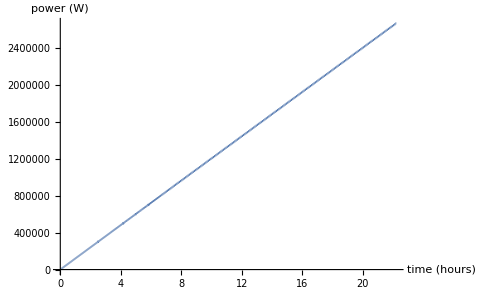

```mathematica
Plot[timepower[3600x], {x,time[0000000]/3600,time[8000000]/3600}, PlotPoints->40000, MaxRecursion->3,AxesLabel->{"time (hours)","power (W)"}]
```

```mathematica
timepowerpiecewise[time_?NumericQ]:=Piecewise[{{timepower[time],time<timeAim},{timepower[time-shortTimeAim], timeAim<time<timeAim+shortTimeAim},{timepower[time-2*shortTimeAim], timeAim+shortTimeAim<time<timeAim+2*shortTimeAim},{timepower[time-3*shortTimeAim], timeAim+2*shortTimeAim<time<timeAim+3*shortTimeAim},{timepower[time-4*shortTimeAim], timeAim+3*shortTimeAim<time<timeAim+4*shortTimeAim},{timepower[time-5*shortTimeAim], timeAim+4*shortTimeAim<time<timeAim+5*shortTimeAim},{timepower[time-6*shortTimeAim], timeAim+5*shortTimeAim<time<timeAim+6*shortTimeAim},{timepower[time-7*shortTimeAim], timeAim+6*shortTimeAim<time<timeAim+7*shortTimeAim}}]
```

```mathematica
timeAim*0.2*8+timeAim
```

780000.

```mathematica
780000./3600
```

216.667

```mathematica
216.66666666666666/12
```

18.0556

```mathematica
timeAim
```

300000.

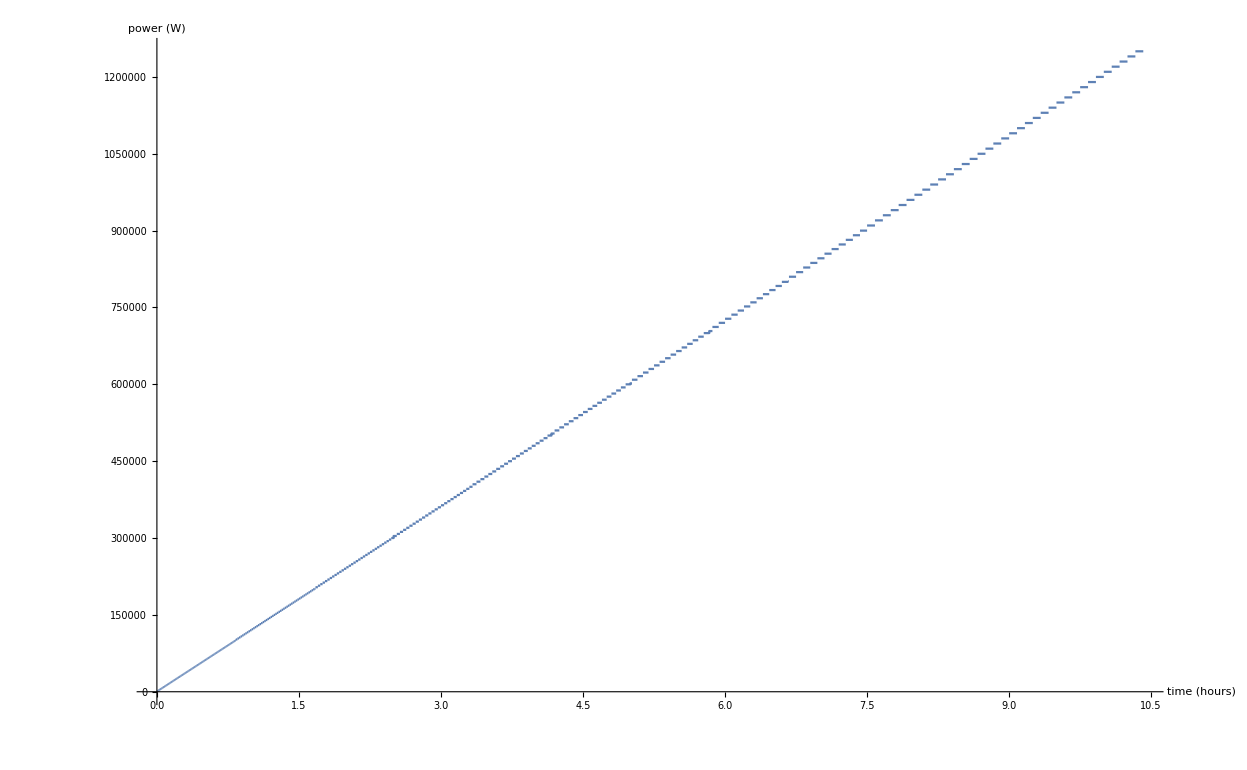

```mathematica
Quiet[Plot[timepowerpiecewise[3600 x], {x,time[0]/3600,(timeAim/8)/3600}, PlotPoints->40000, MaxRecursion->3,AxesLabel->{"time (hours)","power (W)"}]]
```

```mathematica
200/12.
```

16.6667

```mathematica
Clear[eField]
```

```mathematica
eField[x_]:=Sqrt[0.6 timepowerpiecewise[x]]/2449.489742783178*100
```

```mathematica
Table[eField[3600 x],{x,(timeAim-0.01*shortTimeAim)/3600,(timeAim+0.01*shortTimeAim)/3600,0.01}]
```

{99.8999,99.95,99.95,99.95,99.95,99.95,99.95,99.95,99.95,100.,100.,100.,100.,100.,100.,100.,100.,89.4986,89.4986,89.4986,89.4986,89.4986,89.4986,89.4986,89.4986,89.5545,89.5545,89.5545,89.5545,89.5545,89.5545,89.5545,89.5545,89.5545}

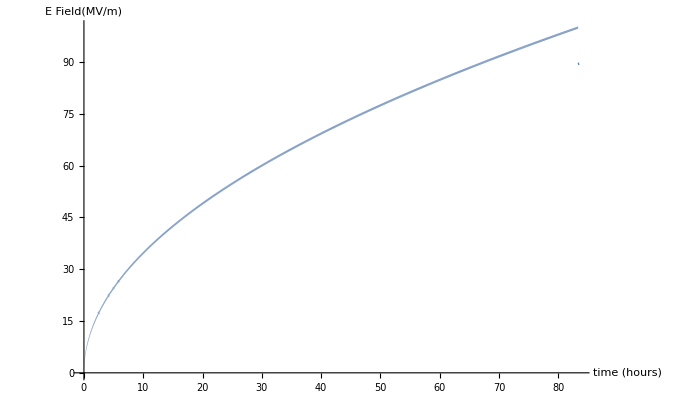

```mathematica
Plot[eField[3600 x], {x,time[0]/3600,(timeAim+0.01*shortTimeAim)/3600}, PlotPoints->40000, MaxRecursion->3,AxesLabel->{"time (hours)","E Field(MV/m)"}]
```

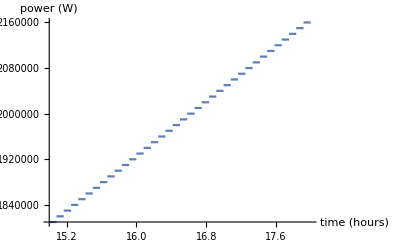

```mathematica
Plot[timepowerpiecewise[3600 x], {x,15,18}, PlotPoints->10000, MaxRecursion->5,AxesLabel->{"time (hours)","power (W)"}]
```

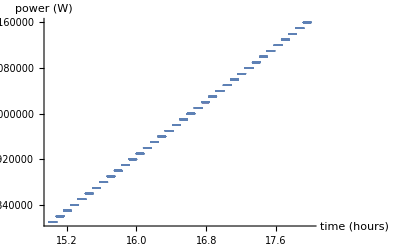

```mathematica
ListPlot[Transpose[{Range[15,18,.0001],timepowerpiecewise[3600 #]&/@Range[15,18,.0001]}],AxesLabel->{"time (hours)","power (W)"}]
```